```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/more_sectors/OnlyBaikov

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a], F1[] -> F[] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

## 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.083152

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}/.m2->1//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √(-((-4+x4) x4)) √(-pp^2-(-1+x4)^2+2 pp (1+x4)))

```mathematica
int1=Integrate[(baik 2Pi^2/.m2->1)/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
(*Total[toint2]*)
int2=Integrate[Simplify[toint2],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2,logs][[1]];
(*Total[toint3]*)
int3=Integrate[toint3,x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=Coefficient[int3,logs][[1]]
(*Quartic polynomial*)
toint4//FullSimplify//PowerExpand// FullSimplify
```

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

-1/(√(-4+x4) √x4 √(pp^2+(-1+x4)^2-2 pp (1+x4)))

```mathematica
EllipticSunrise = 1/(√(4-x4) √x4 √(pp^2+(1-x4)^2-2 pp (1+x4)));
```

```mathematica
(*per=Import["../phi3/2loop/PERIODS/omega0.m"];*)
(*periods={ω0[ρ]->per[[1]] /.F2[g[ρ,a_]] -> ρ^a,ω1[ρ]->per[[2]] /.F2[g[ρ,a_]] -> ρ^a /.F2[g[log,1],g[ρ,m_]]-> L ρ^m};*)
```

```mathematica
periods=Import["./periods/elliptic_sunrise_2l/periods.m"];
```

```mathematica
Collect[Series[Sqrt[3] EllipticSunrise/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x4,1,-1}], {x4,1}]//Expand
periods[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

1+ρ/3+(5 ρ^2)/27+(31 ρ^3)/243+(71 ρ^4)/729+(517 ρ^5)/6561+(11723 ρ^6)/177147

## 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.045843

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=(baik 2 π^3/. m2-> 1)/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2, x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = Coefficient[int2,logs];
int3=Integrate[toint3, x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = Coefficient[int3,logs][[1]];
int4=Integrate[toint4, x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = Coefficient[int4,logs][[1]]
```

$Aborted

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
K3Banana=1/(√(4-x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
periodBanana=Import["./periods/k3_banana_3l/periods.m"];
```

```mathematica
(*
check that the period is corect
*)
```

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

ⅈ+(ⅈ ρ)/16+(7 ⅈ ρ^2)/1024+(ⅈ ρ^3)/1024+(679 ⅈ ρ^4)/4194304+(1969 ⅈ ρ^5)/67108864+(6049 ⅈ ρ^6)/1073741824

Part::partd: Part specification periodBanana⟦1,2⟧ is longer than depth of object.

periodBanana⟦1,2⟧

```mathematica
Collect[Series[4 K3Banana/. pp -> ρ , {ρ,0,6}]//Normal, {ρ},PowerExpand];
Residue[Series[%,{x6,1,-1}], {x6,1}];
Series[%,{x5,0,-1},Assumptions->{Im[x5]>0}]//Normal;
Expand[Residue[%,{x5,0}]]
periodBanana[[1,2]] /. ρ^a_ /; a> 6 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824

## 2 loop Triangle sunrise (difference between 0 and ∞ for the pp expansion) (G operator derived)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4])) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.040774

```mathematica
toint=baik Pi^2 I Sqrt[3]  /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
(* the max cut has *)
toint
(* This is not a hard branch! it doens't have a series expansion for pp -> 0*)
(*  but in z = 1/pp we can *)
Series[toint /. pp -> 1/z, {z,0,5}]//Normal
```

1/(√(-4+pp) √pp)

z+2 z^2+6 z^3+20 z^4+70 z^5

```mathematica
(* If we go to the MUM point, pp -> 1/z and z ~ 0, then we get TWO independent contours, one for x4 ->0 and the other x4  -> ∞ *)
```

```mathematica
(* infinity contour *)
subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,5}]//Normal//PowerExpand //Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[%, {x4,0}]
(* 0  contour, is the max cut! *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
Print[" pole in x4 in 0 "]
Series[%%, {z,0,5},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Print["this one is the max cut"]
Residue[%%, {x4,0}]
```

pole in x4 at infinity

(ⅈ (x4^4 z+x4^3 z^2+2 x4^4 z^2+x4^2 z^3+6 x4^3 z^3+6 x4^4 z^3+x4 z^4+12 x4^2 z^4+30 x4^3 z^4+20 x4^4 z^4+z^5+20 x4 z^5+90 x4^2 z^5+140 x4^3 z^5+70 x4^4 z^5))/(x4^4 √(1+x4) √(-1+3 x4))

z^2+7 z^3+45 z^4+297 z^5

pole in x4 in 0

1/(x4 √(3+2 x4-x4^2))(√3 z+2 √3 z^2+√3 x4 z^2+6 √3 z^3+6 √3 x4 z^3+√3 x4^2 z^3+20 √3 z^4+30 √3 x4 z^4+12 √3 x4^2 z^4+√3 x4^3 z^4+70 √3 z^5+140 √3 x4 z^5+90 √3 x4^2 z^5+20 √3 x4^3 z^5+√3 x4^4 z^5)

this one is the max cut

z+2 z^2+6 z^3+20 z^4+70 z^5

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Print["The following has a pole in x4 ->0 "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
Residue[- % 3, {x4,0}]//Expand
Print["but it does not have any pole in x4 -> ∞ "]
Series[subtop, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand;
Collect[(%/. x4 ->1/x4)/x4/x4 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand, {z}, Simplify]//Together
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal
(* now there is nothing because we cannot find the a series expansion of hard branch type for 1/Sqrt[4 -pp]/Sqrt[pp] *)
```

The following has a pole in x4 ->0

(√3 (x4^6+2 x4^4 z+x4^5 z+6 x4^2 z^2+6 x4^3 z^2+x4^4 z^2+20 z^3+30 x4 z^3+12 x4^2 z^3+x4^3 z^3))/(x4^8 √(3+2 x4-x4^2))

1+(5 z)/9+z^2/3+(55 z^3)/243

but it does not have any pole in x4 -> ∞

(√3 x4+√3 x4^2 z+2 √3 x4^3 z+√3 x4^3 z^2+6 √3 x4^4 z^2+6 √3 x4^5 z^2+√3 x4^4 z^3+12 √3 x4^5 z^3+30 √3 x4^6 z^3+20 √3 x4^7 z^3)/(√(1+x4) √(-1+3 x4))

0

### Differential Operator at z -> ∞

at Differential Operator z→∞

```mathematica
(* infinity contour *)
(*subtop=-baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> 1/z //Simplify//PowerExpand;
(subtop /. x4 -> 1/x4)/x4/x4/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand;
Print[" pole in x4 at infinity"]
Series[%%, {z,0,25}]//Normal//PowerExpand //Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess=Residue[%, {x4,0}]*)
```

pole in x4 at infinity

```mathematica
(*Export["./2loopEasy/gfunctionExpansion.m",functionToGuess]*)
functionToGuess=Import["./2loopEasy/gfunctionExpansion.m"];
```

```mathematica
(*sunriseatinf=Residue[Collect[Series[((Series[subtop x4, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal)/. x4 -> 1/x4)/x4/x4, {x4,0,-1}]//Normal//PowerExpand, {z}, Factor], {x4,0}];*)
```

$Aborted

```mathematica
(*Export["./2loopEasy/sunrise_period_at_inf.m",sunriseatinf]*)
sunriseatinf=Import["./2loopEasy/sunrise_period_at_inf.m"];
```

```mathematica
(*Residue[Series[Series[-subtop x4 Sqrt[3] I /. z ->1/z, {z,0,3},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//PowerExpand, {x4,0,-1}]//Normal//PowerExpand, {x4,0}]//Expand
Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/. ρ^n_ /; n >5 ->0*)
```

```mathematica
maxorderPoly = 3;
maxDerDer= 1;
maxDerInhom = 1;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), sunriseatinf/.z -> ρ];
inhomogFormal = generateAnsatzInhomogFormal[maxorderPoly, maxDerInhom (*max derivative omegas banana*)]
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog]/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1, ρ,20],0]]]//Flatten
(derOp G0[ρ] + inhomogFormal /. sol /. F1[]-> 1//Expand )/.Subscript[a, 0,0]-> 0/. Subscript[a, 0,1]-> 1 /. F1[θ]G0[ρ] -> ρ D[G0[ρ] ,ρ]
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3))

f[ρ] b_(0,0)+b_(1,0) f'[ρ]+ρ (f[ρ] b_(0,1)+b_(1,1) f'[ρ])+ρ^2 (f[ρ] b_(0,2)+b_(1,2) f'[ρ])+ρ^3 (f[ρ] b_(0,3)+b_(1,3) f'[ρ])

{a_(0,2)→-2,a_(0,3)→0,a_(1,0)→0,a_(1,1)→-1,a_(1,2)→4,a_(1,3)→0,b_(0,0)→0,b_(0,1)→0,b_(0,2)→-2/3,b_(0,3)→0,b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→5/3}

-2/3 ρ^2 f[ρ]+ρ G0[ρ]-2 ρ^2 G0[ρ]+5/3 ρ^3 f'[ρ]-ρ^2 G0'[ρ]+4 ρ^3 G0'[ρ]

```mathematica
(* where f above is the sunrise period*)
```

```mathematica
(* we want to normalize by the leading sing *)
ρ G0[z]-2 ρ^2 G0[z]-ρ ρ D[G0[z],z]+4 ρ^2 ρ D[G0[z],z]  + 5/3 dω0sunrise ρ^3 -2/3 ρ^2 ω0sunrise   /. ρ -> z
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z G0[z]-2 z^2 G0[z]-z^2 G0'[z]+4 z^3 G0'[z]

```mathematica
(*G1 =Sqrt[1-4 z]/z G0 *)
(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+z (G1[z] z/Sqrt[1 - 4 z])-2 z^2 (G1[z] z/Sqrt[1 - 4 z])-z^2 D[(G1[z] z/Sqrt[1 - 4 z]),z]+4 z^3 D[(G1[z] z/Sqrt[1 - 4 z]),z]
Collect[%/√(1-4 z)/ z^3, {ω0sunrise, dω0sunrise, _G},Simplify]
```

(5 dω0sunrise z^3)/3-(2 z^2 ω0sunrise)/3+(z^2 G1[z])/(√(1-4 z))-(2 z^3 G1[z])/(√(1-4 z))-z^2 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))+4 z^3 (G1[z]/(√(1-4 z))+(2 z G1[z])/(1-4 z)^(3/2)+(z G1'[z])/(√(1-4 z)))

```mathematica
Solve[(5 dω0sunrise)/(3 √(1-4 z))-(2 ω0sunrise)/(3 √(1-4 z) z)-G1'[z]== 0 ,G1'[z]]
```

{{G1'[z]→(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z)}}

```mathematica
(* shift G2[z] = G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z))*)
```

```mathematica
D[G1[z] - (5 ω0sunrise[z])/(3 √(1-4 z)) ,z]  /. G1'[z]->(5 dω0sunrise z-2 ω0sunrise)/(3 √(1-4 z) z) /. ω0sunrise[z] -> ω0sunrise /.ω0sunrise'[z] -> dω0sunrise // Simplify
```

-(2 (1+z) ω0sunrise)/(3 (1-4 z)^(3/2) z)

```mathematica
(*G -> Sqrt[1-4 z]/z G0   - (5 ω0sunrise[z])/(3 √(1-4 z))*)
(* Satisfies *)
D[G[z],z] ==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)
```

G'[z]==-(2 (1+z) ω0sunrise[z])/(3 (1-4 z)^(3/2) z)

### Differential Operator at pp -> 0 (check that is the same operator)

```mathematica
(* If we don't go to the MUM point, pp -> z and z ~ 0,  we get only one independent contour, because the leading sing. does not admit a series expansion, in fact ... *)
subtop= I Sqrt[3]baik Pi^2/x4 /. {x1 -> 0, x2 -> 0, x3 -> 0}/. pp -> z //Simplify//PowerExpand;
Series[subtop, {z,0,22},Assumptions->{Im[2 (2+x4) z-x4^2 z^2]>0}]//Normal//PowerExpand//Together;
Series[%, {x4,0,-1}, Assumptions->{Im[x4]>0}]//Normal;
functionToGuess = Residue[- % 3, {x4,0}]//Expand;
```

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
nhomog
```

5/3 dω0sunrise ρ^3 F1[]-2/3 ρ^2 ω0sunrise F1[]

```mathematica
Expand[((ρ F1[]-2 ρ^2 F1[]-ρ F1[θ]+4 ρ^2 F1[θ] ) /. ρ -> 1/ρ /. F1[θ]->-F1[θ] )(Expand[F2[]functionToGuess/. z -> ρ] /. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]] )] //.combineOperator//.moveRightPoly /.extractPoly /. zeroOP /. F[]-> 1//Normal;
Series[-5/3 D[(Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]),ρ] (1/ρ) F1[]-2/3 ρ^-2 (Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]) F1[] , {ρ,0,20}] /. F1[]-> 1//Normal;
%%-3 %//Expand
```

(26076257225837913515 ρ^21)/36472996377170786403

```mathematica
(* the operator is the same, the three comes from insisting on normalizing the period to 1. *)
```

## 3 loop Triangle sunrise (G operator derived)

```mathematica
K3Banana=x1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

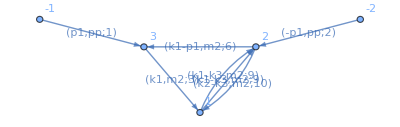

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.038424

```mathematica
toint=baik Pi^3 /(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify//PowerExpand;
```

```mathematica
toint
```

-1/(x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-4+x6) √x6 √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=K3Banana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

x1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/((-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Integrate[PowerExpand[integrand (x5 - 1) /. x5 -> 1 ]//FullSimplify//PowerExpand,x6];
Coefficient[%,Log[x6]]
```

-1/(4 √(-4+pp) √pp)

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
periodBanana=ω0[ρ]/.Import["./periods/k3_banana_3l/periods.m"][[1]];
```

```mathematica
toexpand =integrand Pi^3 (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ π^3)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandroots/expandroots.m",tocheck];*)
expandRoot= Import["./expandroots/expandroots.m"];
```

```mathematica
Print["done"]
(*Series and max cut do not commute *)
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
function/.extractPolySol /. ρ^a_ /; a> 5 -> 0
Series[--I/(4  √(-4+pp) √pp), {pp,0,5}, Assumptions->{Im[pp]>0}]//Normal
```

ReplaceAll::reps: {extractPolySol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

π^3 F2[g[ρ,0]]+1/4 π^3 F2[g[ρ,1]]+(61 π^3 F2[g[ρ,2]])/1024+(29 π^3 F2[g[ρ,3]])/2048+(14179 π^3 F2[g[ρ,4]])/4194304+(6803 π^3 F2[g[ρ,5]])/8388608+(209791 π^3 F2[g[ρ,6]])/1073741824+(202897 π^3 F2[g[ρ,7]])/4294967296+(806157151 π^3 F2[g[ρ,8]])/70368744177664+(783957289 π^3 F2[g[ρ,9]])/281474976710656+(48895535533 π^3 F2[g[ρ,10]])/72057594037927936+(5967176921 π^3 F2[g[ρ,11]])/36028797018963968+(2987552856157 π^3 F2[g[ρ,12]])/73786976294838206464+(182840787091 π^3 F2[g[ρ,13]])/18446744073709551616+(91780437865277 π^3 F2[g[ρ,14]])/37778931862957161709568+(90079830852473 π^3 F2[g[ρ,15]])/151115727451828646838272+(2899849317164781079 π^3 F2[g[ρ,16]])/19807040628566084398385987584+(2851356634479036475 π^3 F2[g[ρ,17]])/79228162514264337593543950336+(179576528476303362415 π^3 F2[g[ρ,18]])/20282409603651670423947251286016+(88419558577649876561 π^3 F2[g[ρ,19]])/40564819207303340847894502572032+(44609838686965626980251 π^3 F2[g[ρ,20]])/83076749736557242056487941267521536+(21992413189630341743933 π^3 F2[g[ρ,21]])/166153499473114484112975882535043072+(173569794750292053460771 π^3 F2[g[ρ,22]])/5316911983139663491615228241121378304+(171319211256944274133693 π^3 F2[g[ρ,23]])/21267647932558653966460912964485513216+(692950520370934114324874569 π^3 F2[g[ρ,24]])/348449143727040986586495598010130648530944-(10092078899117848054497373038575993400461673275022272593 π^3 F2[g[ρ,25]])/2787593149816327892691964784081045188247552/.extractPolySol

1/(8 √pp)+(√pp)/64+(3 pp^(3/2))/1024+(5 pp^(5/2))/8192+(35 pp^(7/2))/262144+(63 pp^(9/2))/2097152

```mathematica
periodBanana=Expand[periodBanana F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] periodBanana+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[periodBanana /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)

## 4 loop banana (period verified with differential eq)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}};
nodes = {{1,0}, {2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6] x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik =Pi^4  baik // FullSimplify;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.044486

```mathematica
maxcutIntegrand=baik /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} // FullSimplify // PowerExpand//FullSimplify
```

ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8)))

```mathematica
toint=-maxcutIntegrand /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,5}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x7  *)
series=Collect[(tmp/. x7 ->1/x7)/x7/x7 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x7,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x7,0}];
tmp=Collect[tmp, {s}, Simplify];
(* Square root, so it has a pole a infinity in x6  *)
series=Collect[(tmp/. x6->1/x6)/x6/x6 , {s},PowerExpand[FullSimplify[#]]&];
tmp=Series[%, {x6,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x6,0}];
tmp=Collect[tmp, {s}, Simplify]
periodsFourLoopBanana = Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. ρ^n_ /; n>5 -> 0
Print[" Yeee "]
```

s+5 s^2+45 s^3+545 s^4+7885 s^5

ρ+5 ρ^2+45 ρ^3+545 ρ^4+7885 ρ^5

Yeee

## 4 loop triangle bubble - sunrise easy (elliptic)

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/((x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^(-ν[6]) x7^ν[7] x8^ν[8] d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6]⋀d[x7]⋀d[x8]))/. eps-> 0] /. s-> pp ;
baik = Pi^4 baik// FullSimplify
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

Drop::drop: Cannot drop positions 1 through 1 in {}.

{-Graphics-,-Graphics-}

"Total runtime= "  0.114514

-1/(√(-(x1-x3)^2+2 (2+x1+x3) x7-x7^2) √(-(x2-x6)^2+2 (2+x2+x6) x7-x7^2) √(-(x4-x6)^2+2 (2+x4+x6) x8-x8^2) √(-pp^2-(1+x5-x8)^2+2 pp (1+x5+x8)))

```mathematica
(* max cut *)
toint=baik  /. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0,x6-> 0}//FullSimplify // PowerExpand// FullSimplify
int1=Integrate[toint, x7];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]
```

-ⅈ/((-4+x7) x7 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

-ⅈ/(4 √(-4+x8) √x8 √(-pp^2-(-1+x8)^2+2 pp (1+x8)))

```mathematica
(*Import["./periods/elliptic_sunrise_2l/periods.m"][[1,2]]/.ρ^n_ /; n> 3 ->0*)
```

```mathematica
(*MAX CUT*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> pp, {pp,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Series[%,{x8,1,-1}, Assumptions->{Im[x8]>0}]//Normal//FullSimplify;
Print[" max cut in pp"]
Residue[%% I 4 Sqrt[3],{x8,1}]//Expand
(*MAX CUT at inf*)
baik/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0, x6 -> 0}//FullSimplify;
Series[% /. pp -> 1/s, {s,0,5}]//Normal//PowerExpand;
Residue[Series[%,{x7,0,-1}]//Normal//FullSimplify, {x7,0}];
Collect[(% /. x8 -> 1/x8)/x8^2, {s}, FullSimplify];
Print[" max cut in s = 1 / pp"]
Residue[Series[%% 4, {x8,0,-1}]//Normal, {x8,0}]
```

max cut in pp

1+pp/3+(5 pp^2)/27+(31 pp^3)/243+(71 pp^4)/729+(517 pp^5)/6561

max cut in s = 1 / pp

s+3 s^2+15 s^3+93 s^4+639 s^5

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Collect[Series[toint, {s,0,3}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
Print["notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞"]
tmp=Collect[tmp, {s}, Simplify] // Together
 (*single pole for x6 -> 0, this goes to max cut*)
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[4 series2,{x6,0}];
(*put back the s*)
Print["this is again the max cut solution, found by taking the pole at 0 :) "]
Collect[s Residue[Series[- tmp2, {x7,0,-1}]//Normal, {x7,0}], {s},FullSimplify]
(* Stupid pole at infinity now !!!!! *)
Print[" by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !"]
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}]
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

notice that now we have a pole in x6 -> 0 but might also have one for x6 ->∞

(ⅈ (1+3 s+15 s^2+93 s^3+s x6+10 s^2 x6+93 s^3 x6+s^2 x6^2+21 s^3 x6^2+s^3 x6^3))/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

this is again the max cut solution, found by taking the pole at 0 :)

s+3 s^2+15 s^3+93 s^4

by sending x6 -> 1/x6, we find something with a pole in x6 ->0, so another contour !

(s^3+s^2 x6+21 s^3 x6+s x6^2+10 s^2 x6^2+93 s^3 x6^2+x6^3+3 s x6^3+15 s^2 x6^3+93 s^3 x6^3)/(x6^3 √(-4+x7) √x7 √(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2))

and this contour give the independent solution

s+12 s^2+145 s^3

```mathematica
(*(* this is correctly the banana, up to the new pole*)
bananaCut=baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
((bananaCut//PowerExpand//FullSimplify//PowerExpand) // Simplify//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
banana4loop=(ⅈ/(√(-4+x6) √x6 √(-x6^2-(-1+x7)^2+2 x6 (1+x7)) √(-pp^2-(-1+x8)^2+2 pp (1+x8)) √(-x7^2-(-1+x8)^2+2 x7 (1+x8))) /. {x6 -> x7, x7 -> x6}/.x6 -> x6+1//FullSimplify)/. 1/Sqrt[a__]:> 1/Sqrt[Simplify[Expand[a]]]
%%/%*)
```

```mathematica
(*more ... *)
```

```mathematica
toint=baik x8/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,15}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

-1/((-4+x7) x7)2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

1/2 (1+4 s+23 s^2+153 s^3+1095 s^4+8188 s^5+63057 s^6+496044 s^7+3965519 s^8+32104596 s^9+262577865 s^10+2165671335 s^11+17987913945 s^12+150302455020 s^13+1262371593183 s^14+10650099838473 s^15)

```mathematica
(* derivative, second kind *)
```

```mathematica
toint=D[baik,pp] /x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0};
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
series=Series[toint, {s,0,6}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal;
Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&];
Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
Coefficient[Series[Residue[%,{x8,0}] , {x6,0,-1}]//Normal,x6,-1]//PowerExpand
Residue[%,{x7,0}]
```

(s+6 s^2+45 s^3+372 s^4+3195 s^5+27918 s^6)/((-4+x7) x7)

1/4 (-s-6 s^2-45 s^3-372 s^4-3195 s^5-27918 s^6)

### Differential Operator at z -> ∞

```mathematica
toint=-baik/x6/. {x1-> 0,x2-> 0,x3-> 0,x4-> 0,x5-> 0} 
(*Collect[Series[toint, {pp,0,1}]//Normal// PowerExpand , {pp}, FullSimplify]*)
(*Expand at the mum point of the four-loop banana*)
toint=toint/s /. pp ->1/s//FullSimplify//PowerExpand;
```

1/(x6 √(4 x7-x7^2) √(-x6^2+2 (2+x6) x7-x7^2) √(-x6^2+2 (2+x6) x8-x8^2) √(-pp^2-(1-x8)^2+2 pp (1+x8)))

```mathematica
tmpsqrt=Collect[Series[E^(-1/2 Normal[Series[Log[-1-s^2 (-1+x8)^2+2 s (1+x8)], {s,0,130},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]<0]]), {s,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Collect[Series[1/(√(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,10},Assumptions-> Im[-s^2 (-1+x8)^2+2 s (1+x8)]≥0], {s},Factor];
Series[tmpsqrt, {s,0,10}]//Normal;
%%+%//Together;*)
```

```mathematica
tmptoint=((toint √(-1-s^2 (-1+x8)^2+2 s (1+x8)) /. x8 ->1/x8)/x8/x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-4 x8-2 x6 x8+x6^2 x8^2) x8
```

-1/(x6 √(-4+x7) √x7 √(-x6^2+4 x7+2 x6 x7-x7^2))

```mathematica
tmpsqrt2=Collect[Series[E^(-1/2 Normal[Series[Log[1-4 x8-2 x6 x8+x6^2 x8^2], {x8,0,140}]]), {x8,0,120}]//Normal, {s}, Factor];
```

```mathematica
(*Series[((Series[1/(√(-(x6-x8)^2+4 x8) √(-1-s^2 (-1+x8)^2+2 s (1+x8))), {s,0,3},Assumptions->Im[-s^2 (-1+x8)^2+2 s (1+x8)]>0]//Normal)/.x8-> 1/x8)/x8/x8 /. 1/Sqrt[a_]:>1/Sqrt[Factor[a]]//PowerExpand, {x8,0,-1}]//Normal
Collect[%,{s},Simplify]*)
```

```mathematica
num=Collect[Coefficient[Series[1/x8 tmpsqrt2 (tmpsqrt/.x8 -> 1/x8), {x8,0,-1}] // Normal , x8,-1], {s},Simplify];
```

```mathematica
tmptoint2=((tmptoint/. x6 -> 1/x6 )/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//PowerExpand)√(1-2 x6 x7-4 x6^2 x7+x6^2 x7^2);
tmpsqrt3=Collect[Series[E^(-1/2 Normal[Series[Log[1-2 x6 x7-4 x6^2 x7+x6^2 x7^2], {x6,0,140}]]), {x6,0,120}]//Normal, {s}, Factor];
num=Coefficient[Collect[Series[tmpsqrt3( num /. x6 -> 1/x6), {x6,0,-1}]//Normal, {s},Factor], x6,-1];
tmptoint3=Collect[((ⅈ/(√(-4+x7) √x7)/. x7 -> 1/x7)/x7/x7 /. 1/Sqrt[a_] :> 1/Sqrt[Factor[a]]//PowerExpand)(num/. x7 -> 1/x7), {s},Normal[ Series[#, {x7,0,-1}, Assumptions->{x7 >4}]]&];
test=Residue[-I %,{x7,0}] /. s -> z;
test = test /. z^n_ /; n> 110 -> 0;
```

```mathematica
(*Export["./4loopEasy/gfunctionExpansion_110orders.m",test]*)
```

```mathematica
(*
series=Collect[Series[toint, {s,0,28}, Assumptions->{s>0 && x8 >0 && x7>0 && x6 >0}]//Normal// PowerExpand , {s}, FullSimplify];
(* Square root, so it has a pole a infinity in x8  *)
series=Collect[Collect[(series/. x8 ->1/x8)/x8/x8 , {s},PowerExpand[FullSimplify[#]]&]/. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify];
tmp=Series[%, {x8,0,-1}, Assumptions->{s>0&& x8 >0 && x7>0 && x6 >0}]//Normal;
tmp=Residue[tmp,{x8,0}];
tmp=Collect[(tmp/. x6 -> 1/x6)/x6/x6 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]] // PowerExpand, {s}, Simplify]//Together;
series2 = Series[tmp, {x6,0,-1}]//Normal//PowerExpand;
tmp2=Residue[series2,{x6,0}]//Expand;
Print["and this contour give the independent solution "]
functionToGuess=Residue[Series[(tmp2 /. x7 -> 1/x7)/x7/x7, {x7,0,-1}]//Normal, {x7,0}];
functionToGuess=functionToGuess /. s -> z *)
(*Export["./4loopEasy/gfunctionExpansion_28orders.m",functionToGuess]*)
```

```mathematica
functionToGuess=Import["./4loopEasy/gfunctionExpansion_110orders.m"];
```

```mathematica
ratio =Collect[Series[ Import["./periods/CY_3_banana_4l/periods.m"][[2,2]]/ Import["./periods/CY_3_banana_4l/periods.m"][[1,2]] /. Log[ρ]-> L, {ρ,0,100}]//Normal, {L},Simplify] /. L -> Log[ρ];
α1 = Series[1/(ρ D[ratio,ρ]),{ρ,0,100}]//Normal;
```

```mathematica
banana4loop = Import["./periods/CY_3_banana_4l/periods.m"][[1,2 ]];
```

```mathematica
banana=Expand[(banana4loop F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dbanana=Expand[(D[banana4loop,ρ]F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
ddbanana=Expand[D[D[banana4loop,ρ],ρ]]F2[]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
dddbanana=Expand[D[D[D[banana4loop,ρ],ρ],ρ]F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1f= Expand[α1 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
α1fsquared= Expand[α1^2 F2[]]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
```

```mathematica
(* move in the preambule *)
generateFunctionForAnsatz[function_] := Module[{sol},
sol=Expand[(function F2[])]/. ρ^n_ F2[] -> F2[g[ρ,n]]/. ρ^a_ F2[]:> F2[g[ρ,a]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]];
Return[sol]
]
generateAnsatzDer[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op},
If[derorder>100, Print["Nein!"]];
f1s=F1/@Table[Table[θ, {i,1,n}], {n,0,100}]  /. F1[List[a___]]:> F1[a];
op=Sum[Sum[Subscript[a, i,j] ρ^j, {j,0,orderpoly}]f1s[[i+1]], {i,0,derorder}];
Return[op]
] 
generateAnsatzInhomog[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*), function_] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[function,{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
] 
generateAnsatzInhomogFormal[orderpoly_, derorder_ (*max order of polynomial, max order of derivative*)] :=Module[{op,functionForAnsatz},
If[derorder>10, Print["Nein!"]];
derivatives= Do[der[i] = D[f[ρ],{ρ,i}], {i,0,10}];
Do[functionForAnsatz[i] = generateFunctionForAnsatz[der[i]], {i,0,10}];
op=Sum[Sum[Subscript[b, i,j] ρ^j, {j,0,orderpoly}]F1[]functionForAnsatz[i], {i,0,derorder}];
op  =  Collect[Expand[op] //. combineOperator //.extractPoly /. zeroOP /. F[]-> 1,ρ, Simplify];
Return[op]
]
```

```mathematica
maxorderPoly = 3;
maxDerDer= 1;
maxDerInhom = 3;
derOp = generateAnsatzDer[maxorderPoly, maxDerDer]
inhomog = generateAnsatzInhomog[maxorderPoly, maxDerInhom (*max derivative omegas banana*), banana4loop];
derApplied=Expand[derOp generateFunctionForAnsatz[functionToGuess/. z-> ρ]] //.combineOperator//.moveRightPoly//.moveRightLog//.zeroOP //. extractPoly//.zeroOP /. F[]-> 1;
sol=Solve[Thread[Equal[CoefficientList[Expand[derApplied + inhomog], ρ,30],0]]]
```

F1[] (a_(0,0)+ρ a_(0,1)+ρ^2 a_(0,2)+ρ^3 a_(0,3))+F1[θ] (a_(1,0)+ρ a_(1,1)+ρ^2 a_(1,2)+ρ^3 a_(1,3))

{{a_(0,0)→0,a_(0,1)→0,a_(0,2)→0,a_(0,3)→0,a_(1,0)→0,a_(1,1)→0,a_(1,2)→0,a_(1,3)→0,b_(0,0)→0,b_(0,1)→0,b_(0,2)→0,b_(0,3)→0,b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→0,b_(2,3)→0,b_(3,0)→0,b_(3,1)→0,b_(3,2)→0,b_(3,3)→0}}

```mathematica
(* second derivative of period not needed ? *)
maxorder=5
ansatzDer=Sum[a[i] ρ^i F1[], {i,0,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,0,maxorder}](*+ Sum[c[i]F1[θ,θ] ρ^i, {i,1,maxorder}] + Sum[d[i]F1[θ,θ,θ] ρ^i, {i,1,maxorder}]+Sum[e[i]F1[θ,θ,θ,θ] ρ^i, {i,1,maxorder}]*) ;
inhomog=   Sum[f[i]ρ^i , {i,0,maxorder}]F1[] banana+  Sum[g[i]ρ^i , {i, 0,maxorder}]F1[]dbanana+Sum[h[i]ρ^i , {i, 0,maxorder}]F1[]ddbanana+Sum[ii[i]ρ^i , {i, 0,maxorder}]F1[]dddbanana(*+
Sum[l[i]ρ^i , {i, 0,maxorder}]F1[]α1+Sum[m[i]ρ^i , {i, 0,maxorder}]F1[]α1fsquared*)//Expand;
```

5

```mathematica
tmpfunctionToguess=(Expand[(functionToGuess F2[] /. z ->ρ)]/. ρ^n_ F2[] -> F2[g[ρ,n]] /. ρ F2[] -> F2[g[ρ,1]]  /. F2[]  -> F2[g[ρ,0]]);
sol=Equal[CoefficientList[(ansatzDer tmpfunctionToguess+inhomog // Expand) //. combineOperator //.moveRightPoly//.extractPoly /. zeroOP /. F[]-> 1 // PowerExpand,ρ,60],0]//Solve//Flatten
```

{a[0]→0,a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→0,b[0]→0,b[1]→0,b[2]→0,b[3]→0,b[4]→0,b[5]→0,f[0]→0,f[1]→0,f[2]→0,f[3]→0,f[4]→0,f[5]→0,g[0]→0,g[1]→0,g[2]→0,g[3]→0,g[4]→0,g[5]→0,h[0]→0,h[1]→0,h[2]→0,h[3]→0,h[4]→0,h[5]→0,ii[0]→0,ii[1]→0,ii[2]→0,ii[3]→0,ii[4]→0,ii[5]→0}

```mathematica
operder=ansatzDer /. sol /. a[1] -> 1  
nhomog=   Sum[e[i]ρ^i , {i,1,maxorder}]F1[] ω0sunrise+  Sum[f[i]ρ^i , {i,0,maxorder}]F1[]dω0sunrise /. sol  /. a[1]-> 1//Expand
```

0

ρ ω0sunrise e[1] F1[]+ρ^2 ω0sunrise e[2] F1[]+ρ^3 ω0sunrise e[3] F1[]+ρ^4 ω0sunrise e[4] F1[]

## 4 loop triangle bubble - sunrise hard (K3 banana)

```mathematica
SetAttributes[sp,Orderless]
```

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
```

{{{{1,2},m2},{{1,2},m2},{{2,3},m2},{{2,3},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

```mathematica
(* First two loops, two loop sunrise, loop momenta k3, k4 *)
(*  P1 = p1+k1 
(k3)^2-m2, (k3+k4)^2-m2, (k4 + P1)^2-m2
*)
propfirstloop={sp[k3,k3]-m2,
sp[k3,k3] +2sp[k3,k4] + sp[k4,k4]-m2,
sp[k4,k4] + pp + k1k1 + 2 k1p1 +2 sp[k4,P1]-m2, sp[k4,P1], sp[k3,P1]}
(**)
sps= Union@Cases[propfirstloop,_sp,∞];
(*physical props are x1, x2, x3*)
isptoprop=Solve[Thread[Equal[propfirstloop , {x1,x2,x3, x40,x41}]],sps]//Flatten;
```

{-m2+sp[k3,k3],-m2+sp[k3,k3]+2 sp[k3,k4]+sp[k4,k4],k1k1+2 k1p1-m2+pp+sp[k4,k4]+2 sp[k4,P1],sp[k4,P1],sp[k3,P1]}

```mathematica
external = {P1};
allmomenta = {P1,k3,k4};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=%/. sp[P1,P1]-> pp + k1k1 + 2 k1p1/. isptoprop//Simplify;
baik=detInternalMomenta^((d-2-1-1)/2); (* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det ;
mat2 =mat2/. sp[P1,P1]-> pp + k1k1 + 2 k1p1;
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop ;
baik=baik  detExternalMomenta^((2-d)/2) ;(* (1+E-d)/2 , E independent external momenta *)
firstLoopBaik = baik;
```

```mathematica
(*firstLoopBaik /. d-> 2 /. {x1->0, x2->0,x3->0} // FullSimplify
Integrate[%,x41]//TrigToExp;
(Coefficient[%,Log[1-(ⅈ √(-k1k1-2 k1p1+m2-pp-2 x40) (x40+2 x41))/(√(k1k1^3+8 k1p1^3-3 m2^2 pp+2 m2 pp^2+pp^3+4 m2 pp x40+4 pp^2 x40+3 m2 x40^2+5 pp x40^2+2 x40^3+4 k1p1^2 (2 m2+3 pp+4 x40)+k1k1^2 (6 k1p1+2 m2+3 pp+4 x40)+2 k1p1 (-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40))+k1k1 (12 k1p1^2-3 m2^2+3 pp^2+8 pp x40+5 x40^2+4 m2 (pp+x40)+4 k1p1 (2 m2+3 pp+4 x40))))]] //FullSimplify)/.pp->-k1k1-2 k1p1+ PP*)
```

```mathematica
firstLoopBaik/.d-> 10//Variables
```

{k1k1,k1p1,pp,m2,x1,x40,x3,x2,x41}

```mathematica
(* Third loop, I have k1, k1+k2,  k1.p1 --> triangle kinematics *)
(*  
(k1)^2-m2, (k1+k2)^2-m2, (k1 + p1)^2-m2
*)
```

```mathematica
propsecondloop={sp[k1,k1]-m2,
sp[k1,k1] +2 sp[k1,k2] + k2k2-m2,
(* unphysical one *) pp +2 sp[p1,k1]+ sp[k1,k1]}
(*physical prop are 5 and 6*)
isptoprop=Thread[Equal[propsecondloop , {x4,x5,x42}]]//Solve//Flatten
external = {k2,p1};
allmomenta = {p1,k1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,3}, {j,1,3}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop;
(*physical prop are 5 and 6*)
baik2=detInternalMomenta^((d-1-2-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. sp[k2,k2] -> k2k2 /.sp[k2,p1] -> k2p1/. isptoprop 
baik2=baik2  detExternalMomenta^((1+2-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
```

{-m2+sp[k1,k1],k2k2-m2+sp[k1,k1]+2 sp[k1,k2],pp+sp[k1,k1]+2 sp[k1,p1]}

{sp[k1,k1]→m2+x4,sp[k1,k2]→-k2k2/2-x4/2+x5/2,sp[k1,p1]→-m2/2-pp/2-x4/2+x42/2}

-sp[k2,p1]^2+sp[k2,k2] sp[p1,p1]

-k2p1^2+k2k2 pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]}/.isptoprop;
secondLoopBaik =baik2/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
```

```mathematica
secondLoopBaik/.d-> 20//Variables
```

{k2k2,k2p1,m2,pp,x4,x42,x5}

```mathematica
(*
k2^2, and isp k2.p1, bubble kinematics
*)
```

```mathematica
propthirdloop={sp[k2,k2]-m2,sp[k2,p1]}
isptoprop=Thread[Equal[propthirdloop , {x6,x43}]]//Solve//Flatten
external = {p1};
allmomenta = {p1,k2};
mat=Table[sp[allmomenta[[i]], allmomenta[[j]]], {i,1,2}, {j,1,2}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det;
detInternalMomenta=% /. sp[p1,p1]-> pp/. isptoprop;
baik2=detInternalMomenta^((d-1-1-1)/2);(* (d-L-E-1)/2, L loops, E independent external momenta *)
mat2=Table[sp[external[[i]], external[[j]]], {i,1,1}, {j,1,1}] //. {sp[a_+c_,b_]-> sp[a,b] + sp[c,b] }//Det 
detExternalMomenta=% /. sp[p1,p1]-> pp /. isptoprop 
baik2=baik2  detExternalMomenta^((1+1-d)/2);(* (1+E-d)/2 ,E independent external momenta *)
thirdLoopBaik = baik2;
```

{-m2+sp[k2,k2],sp[k2,p1]}

{sp[k2,k2]→m2+x6,sp[k2,p1]→x43}

sp[p1,p1]

pp

```mathematica
firstLoopBaik =firstLoopBaik/. {k1k1-> sp[k1,k1], k1p1 ->sp[k1,p1]};
secondLoopBaik  = secondLoopBaik/. {k2k2 -> sp[k2,k2], k2p1-> sp[k2,p1]}/.isptoprop;
```

```mathematica
(*physical props are x1, x2, x3, x4,x5,x6*)
baik = firstLoopBaik secondLoopBaik thirdLoopBaik /. {x40-> x7,x41->x8,x42->x9,x43->x10} /. m2->1;
Variables[baik/. d-> 2]
```

{x1,x7,x8,pp,x3,x4,x9,x2,x10,x5,x6}

```mathematica
baikd2=baik /. d-> 2//FullSimplify
```

16/((4 x10^2 (1+x4)+pp^2 (1+x6)-2 x10 (1+x4-x5+x6) (1+x4-x9)+(1+x6) (1+x4-x9)^2+pp (-1+x4^2-2 x5-2 x4 x5+(x5-x6)^2-2 x10 (1+x4-x5+x6)-2 x9-2 x6 x9)) (4 x8^2 (1+x3-x9)+(x1^2-2 x1 (1+x2)+(-3+x2) (1+x2)) x9+(x3-x9) (-2-2 x1-2 x2+x3-x9) x9+4 x7^2 (1+x1-2 x8+x9)+4 x7 (-2 x8^2+x8 (1+x1-x2+x3-x9)+x9 (1+x1+x2-x3+x9))))

```mathematica
maxcut = baikd2 /. {x1->0,x2-> 0,x3->0,x4->0,x5->0,x6->0}//FullSimplify;
```

```mathematica
int1=Collect[Integrate[maxcut ,x7]//TrigToExp, _Log, PowerExpand];
logs = Union@Cases[int1, _Log, ∞];
toint2=Coefficient[int1, logs][[1]]//FullSimplify
int2 = Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2, _Log, ∞];
toint3=Coefficient[int2, logs][[1]] /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

-(4 ⅈ)/(√(-1+2 x8-x9) √(-((3+2 x8-x9) (x8^2-x9))) (pp^2+4 x10^2+2 x10 (-1+x9)+(-1+x9)^2-pp (1+2 x10+2 x9)))

-(2 ⅈ)/(√(3+2 x8-x9) √(x8^2-x9) √(6 x8-3 (1+x9)) √(pp^2+(-1+x9)^2-2 pp (1+x9)))

```mathematica
K3banana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6))) /. {x6 -> x9, x5 -> x8} //Expand // FullSimplify
((toint3 Sqrt[3] /2(-I)/. m2->1 //Expand // FullSimplify) /. x8 -> x8/2  /.x8 -> x8 -3 + x9//FullSimplify // PowerExpand//FullSimplify//PowerExpand ) /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]/.x8 -> x8 +4 /. x8 -> -x8 /. 1/Sqrt[a_]:> 1/Sqrt[Factor[a]]//FullSimplify//PowerExpand
```

1/(√(-4+x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

(2 ⅈ)/(√(4-x8) √x8 √(pp^2+(-1+x9)^2-2 pp (1+x9)) √(x8^2+(-1+x9)^2-2 x8 (1+x9)))

```mathematica
(*(Series[K3banana (-4), {pp,0,3}]//Normal //PowerExpand) /. x9 -> x9 +1;
Collect[Series[(%), {x9,0,-1}], {x9}, Simplify];
Collect[Residue[%, {x9,0}], {pp},PowerExpand[Simplify[#]]&];
Residue[Series[%, {x8,0,-1}], {x8,0}] // Expand
Import["./periods/k3_banana_3l/periods.m"][[1,2]] /. ρ^n_ /; n> 5 -> 0*)
```

```mathematica
(*cut selecting the banana*)
```

```mathematica
bananaCut=baikd2/x4 /. m2->1 /. {x1->0, x2->0, x3->0, x5->0, x6->0} // Simplify
```

16/(x4 (pp^2+4 x10^2 (1+x4)+pp (-1+x4^2-2 x10 (1+x4)-2 x9)-2 x10 (1+x4) (1+x4-x9)+(1+x4-x9)^2) (x7^2 (4-8 x8+4 x9)+4 x7 (x8-2 x8^2+x9-x8 x9+x9^2)+(-1+x9) (-4 x8^2+x9 (3+x9))))

```mathematica
int1=Integrate[bananaCut,x7]//TrigToExp;
logs = Union@Cases[int1,_Log,∞];
toint2=Coefficient[int1,logs][[1]];
int2=Integrate[toint2,x10]//TrigToExp;
logs = Union@Cases[int2,_Log,∞];
toint3=Coefficient[int2,logs][[1]]//Simplify;
```

```mathematica
tmp1=Collect[Series[toint3  3(-I)/2 /Sqrt[3]/. pp -> 1/s, {s,0,10}]//Normal//PowerExpand, {s},Simplify];
(*single pole in x4*)
tmp2=Collect[Residue[Series[tmp1, {x4,0,-1}, Assumptions->{Im[x4]<0}]//Normal, {x4,0}], {s}, PowerExpand[FullSimplify[#]]&];
tmp2=((tmp2 /. x8 -> x8 +1/2 x9 //Simplify) /. 1/Sqrt[a_] :> 1/Sqrt[Simplify[a]] );
tmp2=(tmp2 /. x9 -> 1/x9)/x9/x9 /. 1/Sqrt[a_]:> 1/Sqrt[PowerExpand[FullSimplify[a]]]//PowerExpand;
tmp3=Collect[Residue[Series[tmp2, {x9,0,-1}]//Normal, {x9,0}], {s},Simplify];
Residue[Series[(tmp3 /. x8 -> 1/x8)/x8/x8, {x8,0,-1}]//Normal, {x8,0}]
```

s+4 s^2+28 s^3+256 s^4+2716 s^5+31504 s^6+387136 s^7+4951552 s^8+65218204 s^9+878536624 s^10

### Integral families

```mathematica
(* easy triangle bubble sunrise *)
(*
integralfamilies:-name:topoA
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1+p1",m2]
-["k1+k2",m2]
-["k2",m2]
-["k2+k3",m2]
-["k4",m2]
-["k3+k4",m2]
-{bilinear:[["k1","k2"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
# cut_propagators:[1,2,3,4,5,6]
*)

(* difficult triangle sunrise bubble  *)
(* 
integralfamilies:-name:topoB
loop_momenta:[k1,k2,k3,k4]
propagators:-["k1",m2]
-["k1+p1+k3",m2]
-["k3+k4",m2]
-["k4",m2]
-["k1+k2",m2]
-["k2",m2]
-{bilinear:[["k3","p1"],0]}
-{bilinear:[["k1","k3"],0]}
-{bilinear:[["k1","k4"],0]}
-{bilinear:[["k3","k3"],0]}
-{bilinear:[["k2","p1"],0]}
-{bilinear:[["k2","k3"],0]}
-{bilinear:[["k4","p1"],0]}
-{bilinear:[["k2","k4"],0]}
cut_propagators:[1,2,3,4,5,6]
*)
```